# Blatt 2

```mathematica
ClearAll["Global`*"]
```

## Import Data

```mathematica
yrawData={40,85,92,62,25,19,7,4 ,2}
ydata=yrawData/Total[yrawData]
xdata=Range[0,8]
```

{40,85,92,62,25,19,7,4,2}

{5/42,85/336,23/84,31/168,25/336,19/336,1/48,1/84,1/168}

{0,1,2,3,4,5,6,7,8}

## Poisson Distribution

```mathematica
μ=2.148;
```

```mathematica
dist=PoissonDistribution[μ]
```

PoissonDistribution[2.148]

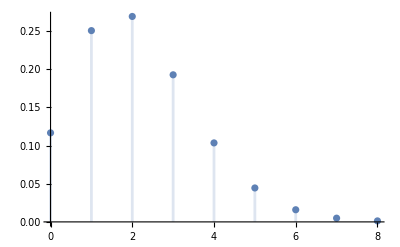

```mathematica
DiscretePlot[PDF[dist][x],{x,0,8}]
```

```mathematica
exportTab={xdata,yrawData,N@ydata,Table[PDF[dist][x],{x,xdata}]};
```

```mathematica
Grid[exportTab]//TeXForm//CopyToClipboard
```

```mathematica
expectedTab=Table[PDF[dist][x],{x,xdata}]
```

{0.116717,0.250709,0.269261,0.192791,0.103529,0.044476,0.0159224,0.0048859,0.00131187}

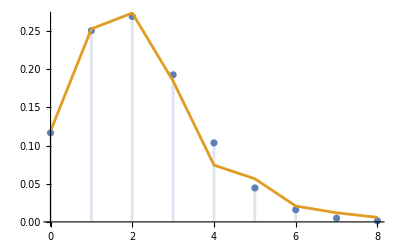

```mathematica
Show[DiscretePlot[PDF[dist][x],{x,0,8}],ListLinePlot[Transpose[{xdata,ydata}],PlotStyle->ColorData[97,2]]]
```

## Chi Squared Test

```mathematica
χ2=Sum[(ydata[[i]]-expectedTab[[i]])^2/expectedTab[[i]],{i,1,Length[ydata]}]
```

0.0399806

```mathematica
Sum[(ydata[[i]]-expectedTab[[i]])^2/expectedTab[[i]],{i,1,Length[ydata]}]
```

0.0399806

```mathematica
expr=Hold[(Evaluate[ydata[[1]]]-Evaluate[expectedTab[[1]]])^2/Evaluate[expectedTab[[1]]]]
```

Hold[(Evaluate[ydata⟦1⟧]-Evaluate[expectedTab⟦1⟧])^2/Evaluate[expectedTab⟦1⟧]]

### String

```mathematica
strTab=Table["\\frac{("<>ToString[N[ydata[[i]]]]<>" - "<>ToString@N[expectedTab[[i]]]<>")^2}{"<>ToString[N[expectedTab[[i]]]]<>"}",{i,1,Length[ydata]}];
```

```mathematica
StringRiffle[strTab,"+"]//CopyToClipboard
```

```mathematica
ReleaseHold@Map[Hold,expr,{2}]
```

Hold[(Evaluate[ydata⟦1⟧]-Evaluate[expectedTab⟦1⟧])^2] Hold[1/Evaluate[expectedTab⟦1⟧]]

```mathematica
ν=7;
dist2=ChiSquareDistribution[ν]
```

ChiSquareDistribution[7]

```mathematica
1-CDF[dist2][χ2]
```

1.